# Контролна работа №2 II вариант Фак. №2001261051

## Задача 1

## Задача 2: Дадена е началната задача за ОДУ: y’ = y - ln(x^2 + 1) + (2x)/(x^2 + 1) + b, y(a) = a + b, x ϵ [a, a + 1]

### a) Да се намери точното решение на задачата

Търсим точно решение :

```mathematica
Clear[x,y]
DSolve[{y'[x]==y[x]-Log[x^2+1]+(2x)/(x^2+1)+1, y[5]==6}, y[x],x]
```

{{y[x]→(-ⅇ^5+7 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5}}

Визуализация на точно решение:

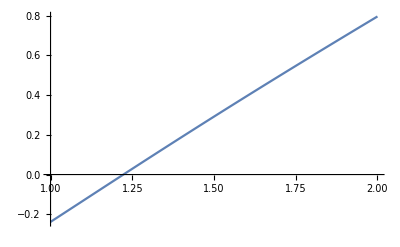

```mathematica
yt[x_]:=(-ⅇ^5+7 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
Plot[yt[x], {x, 1,2}]
```

### б) По метод на Рунге-Кута с четири междинни точки да се реши приближено задачата със стъпка (h) 0.02. Запишете резултатите в таблица. Сравнете с точното решение.

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална  грешка е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

i = 0, x_i = 5., y_i = 6., k1 = , 0.0825304, k2 = 0.0832647, k3 = 0.083272, k4 = 0.084014, y_точно = 6., Истинска грешка = 8.88178×10^-16

i = 1, x_i = 5.02, y_i = 6.08327, k1 = , 0.0840139, k2 = 0.0847634, k3 = 0.0847709, k4 = 0.0855282, y_точно = 6.08327, Истинска грешка = 9.73968×10^-11

i = 2, x_i = 5.04, y_i = 6.16804, k1 = , 0.0855282, k2 = 0.0862932, k3 = 0.0863008, k4 = 0.0870738, y_точно = 6.16804, Истинска грешка = 1.98805×10^-10

i = 3, x_i = 5.06, y_i = 6.25434, k1 = , 0.0870738, k2 = 0.0878546, k3 = 0.0878624, k4 = 0.0886514, y_точно = 6.25434, Истинска грешка = 3.04344×10^-10

i = 4, x_i = 5.08, y_i = 6.3422, k1 = , 0.0886514, k2 = 0.0894484, k3 = 0.0894564, k4 = 0.0902617, y_точно = 6.3422, Истинска грешка = 4.14139×10^-10

i = 5, x_i = 5.1, y_i = 6.43165, k1 = , 0.0902616, k2 = 0.0910751, k3 = 0.0910832, k4 = 0.0919052, y_точно = 6.43165, Истинска грешка = 5.2832×10^-10

i = 6, x_i = 5.12, y_i = 6.52273, k1 = , 0.0919051, k2 = 0.0927354, k3 = 0.0927437, k4 = 0.0935826, y_точно = 6.52273, Истинска грешка = 6.47018×10^-10

i = 7, x_i = 5.14, y_i = 6.61547, k1 = , 0.0935826, k2 = 0.09443, k3 = 0.0944384, k4 = 0.0952947, y_точно = 6.61547, Истинска грешка = 7.70368×10^-10

i = 8, x_i = 5.16, y_i = 6.70991, k1 = , 0.0952946, k2 = 0.0961595, k3 = 0.0961682, k4 = 0.0970421, y_точно = 6.70991, Истинска грешка = 8.98511×10^-10

i = 9, x_i = 5.18, y_i = 6.80607, k1 = , 0.097042, k2 = 0.0979247, k3 = 0.0979335, k4 = 0.0988255, y_точно = 6.80607, Истинска грешка = 1.03159×10^-9

i = 10, x_i = 5.2, y_i = 6.904, k1 = , 0.0988254, k2 = 0.0997263, k3 = 0.0997353, k4 = 0.100646, y_точно = 6.904, Истинска грешка = 1.16974×10^-9

i = 11, x_i = 5.22, y_i = 7.00374, k1 = , 0.100646, k2 = 0.101565, k3 = 0.101574, k4 = 0.102503, y_точно = 7.00374, Истинска грешка = 1.31313×10^-9

i = 12, x_i = 5.24, y_i = 7.10531, k1 = , 0.102503, k2 = 0.103442, k3 = 0.103451, k4 = 0.104399, y_точно = 7.10531, Истинска грешка = 1.4619×10^-9

i = 13, x_i = 5.26, y_i = 7.20875, k1 = , 0.104399, k2 = 0.105357, k3 = 0.105366, k4 = 0.106334, y_точно = 7.20875, Истинска грешка = 1.61622×10^-9

i = 14, x_i = 5.28, y_i = 7.31412, k1 = , 0.106334, k2 = 0.107311, k3 = 0.107321, k4 = 0.108309, y_точно = 7.31412, Истинска грешка = 1.77624×10^-9

i = 15, x_i = 5.3, y_i = 7.42144, k1 = , 0.108309, k2 = 0.109306, k3 = 0.109316, k4 = 0.110324, y_точно = 7.42144, Истинска грешка = 1.94213×10^-9

i = 16, x_i = 5.32, y_i = 7.53075, k1 = , 0.110324, k2 = 0.111342, k3 = 0.111352, k4 = 0.11238, y_точно = 7.53075, Истинска грешка = 2.11408×10^-9

i = 17, x_i = 5.34, y_i = 7.6421, k1 = , 0.11238, k2 = 0.113419, k3 = 0.11343, k4 = 0.114479, y_точно = 7.6421, Истинска грешка = 2.29224×10^-9

i = 18, x_i = 5.36, y_i = 7.75552, k1 = , 0.114479, k2 = 0.115539, k3 = 0.11555, k4 = 0.116621, y_точно = 7.75552, Истинска грешка = 2.4768×10^-9

i = 19, x_i = 5.38, y_i = 7.87107, k1 = , 0.116621, k2 = 0.117703, k3 = 0.117714, k4 = 0.118807, y_точно = 7.87107, Истинска грешка = 2.66795×10^-9

i = 20, x_i = 5.4, y_i = 7.98878, k1 = , 0.118807, k2 = 0.119911, k3 = 0.119922, k4 = 0.121038, y_точно = 7.98878, Истинска грешка = 2.86587×10^-9

i = 21, x_i = 5.42, y_i = 8.1087, k1 = , 0.121038, k2 = 0.122165, k3 = 0.122176, k4 = 0.123314, y_точно = 8.1087, Истинска грешка = 3.07077×10^-9

i = 22, x_i = 5.44, y_i = 8.23087, k1 = , 0.123314, k2 = 0.124464, k3 = 0.124476, k4 = 0.125637, y_точно = 8.23087, Истинска грешка = 3.28285×10^-9

i = 23, x_i = 5.46, y_i = 8.35534, k1 = , 0.125637, k2 = 0.126811, k3 = 0.126822, k4 = 0.128008, y_точно = 8.35534, Истинска грешка = 3.5023×10^-9

i = 24, x_i = 5.48, y_i = 8.48216, k1 = , 0.128008, k2 = 0.129205, k3 = 0.129217, k4 = 0.130427, y_точно = 8.48216, Истинска грешка = 3.72934×10^-9

i = 25, x_i = 5.5, y_i = 8.61138, k1 = , 0.130427, k2 = 0.131649, k3 = 0.131661, k4 = 0.132896, y_точно = 8.61138, Истинска грешка = 3.96419×10^-9

i = 26, x_i = 5.52, y_i = 8.74303, k1 = , 0.132896, k2 = 0.134143, k3 = 0.134155, k4 = 0.135415, y_точно = 8.74303, Истинска грешка = 4.20706×10^-9

i = 27, x_i = 5.54, y_i = 8.87718, k1 = , 0.135415, k2 = 0.136688, k3 = 0.1367, k4 = 0.137986, y_точно = 8.87718, Истинска грешка = 4.45819×10^-9

i = 28, x_i = 5.56, y_i = 9.01388, k1 = , 0.137986, k2 = 0.139284, k3 = 0.139297, k4 = 0.140609, y_точно = 9.01388, Истинска грешка = 4.71782×10^-9

i = 29, x_i = 5.58, y_i = 9.15317, k1 = , 0.140609, k2 = 0.141934, k3 = 0.141947, k4 = 0.143286, y_точно = 9.15317, Истинска грешка = 4.98617×10^-9

i = 30, x_i = 5.6, y_i = 9.29512, k1 = , 0.143286, k2 = 0.144638, k3 = 0.144652, k4 = 0.146018, y_точно = 9.29512, Истинска грешка = 5.2635×10^-9

i = 31, x_i = 5.62, y_i = 9.43976, k1 = , 0.146018, k2 = 0.147397, k3 = 0.147411, k4 = 0.148805, y_точно = 9.43976, Истинска грешка = 5.55006×10^-9

i = 32, x_i = 5.64, y_i = 9.58717, k1 = , 0.148805, k2 = 0.150213, k3 = 0.150227, k4 = 0.151649, y_точно = 9.58717, Истинска грешка = 5.84611×10^-9

i = 33, x_i = 5.66, y_i = 9.73739, k1 = , 0.151649, k2 = 0.153086, k3 = 0.1531, k4 = 0.154552, y_точно = 9.73739, Истинска грешка = 6.15192×10^-9

i = 34, x_i = 5.68, y_i = 9.89049, k1 = , 0.154552, k2 = 0.156018, k3 = 0.156032, k4 = 0.157513, y_точно = 9.89049, Истинска грешка = 6.46775×10^-9

i = 35, x_i = 5.7, y_i = 10.0465, k1 = , 0.157513, k2 = 0.159009, k3 = 0.159024, k4 = 0.160536, y_точно = 10.0465, Истинска грешка = 6.79389×10^-9

i = 36, x_i = 5.72, y_i = 10.2055, k1 = , 0.160535, k2 = 0.162062, k3 = 0.162077, k4 = 0.163619, y_точно = 10.2055, Истинска грешка = 7.13062×10^-9

i = 37, x_i = 5.74, y_i = 10.3676, k1 = , 0.163619, k2 = 0.165177, k3 = 0.165192, k4 = 0.166766, y_точно = 10.3676, Истинска грешка = 7.47825×10^-9

i = 38, x_i = 5.76, y_i = 10.5328, k1 = , 0.166766, k2 = 0.168355, k3 = 0.168371, k4 = 0.169977, y_точно = 10.5328, Истинска грешка = 7.83707×10^-9

i = 39, x_i = 5.78, y_i = 10.7012, k1 = , 0.169976, k2 = 0.171598, k3 = 0.171614, k4 = 0.173253, y_точно = 10.7012, Истинска грешка = 8.20738×10^-9

i = 40, x_i = 5.8, y_i = 10.8728, k1 = , 0.173253, k2 = 0.174907, k3 = 0.174924, k4 = 0.176596, y_точно = 10.8728, Истинска грешка = 8.58952×10^-9

i = 41, x_i = 5.82, y_i = 11.0477, k1 = , 0.176596, k2 = 0.178284, k3 = 0.178301, k4 = 0.180007, y_точно = 11.0477, Истинска грешка = 8.9838×10^-9

i = 42, x_i = 5.84, y_i = 11.226, k1 = , 0.180007, k2 = 0.181729, k3 = 0.181747, k4 = 0.183487, y_точно = 11.226, Истинска грешка = 9.39057×10^-9

i = 43, x_i = 5.86, y_i = 11.4077, k1 = , 0.183487, k2 = 0.185245, k3 = 0.185263, k4 = 0.187039, y_точно = 11.4077, Истинска грешка = 9.81015×10^-9

i = 44, x_i = 5.88, y_i = 11.593, k1 = , 0.187039, k2 = 0.188832, k3 = 0.18885, k4 = 0.190662, y_точно = 11.593, Истинска грешка = 1.02429×10^-8

i = 45, x_i = 5.9, y_i = 11.7818, k1 = , 0.190662, k2 = 0.192493, k3 = 0.192511, k4 = 0.19436, y_точно = 11.7818, Истинска грешка = 1.06892×10^-8

i = 46, x_i = 5.92, y_i = 11.9743, k1 = , 0.19436, k2 = 0.196227, k3 = 0.196246, k4 = 0.198133, y_точно = 11.9743, Истинска грешка = 1.11494×10^-8

i = 47, x_i = 5.94, y_i = 12.1706, k1 = , 0.198132, k2 = 0.200038, k3 = 0.200057, k4 = 0.201982, y_точно = 12.1706, Истинска грешка = 1.16239×10^-8

i = 48, x_i = 5.96, y_i = 12.3706, k1 = , 0.201982, k2 = 0.203926, k3 = 0.203946, k4 = 0.20591, y_точно = 12.3706, Истинска грешка = 1.2113×10^-8

i = 49, x_i = 5.98, y_i = 12.5746, k1 = , 0.20591, k2 = 0.207894, k3 = 0.207913, k4 = 0.209918, y_точно = 12.5746, Истинска грешка = 1.26173×10^-8

i = 50, x_i = 6., y_i = 12.7825, k1 = , 0.209917, k2 = 0.211942, k3 = 0.211962, k4 = 0.214007, y_точно = 12.7825, Истинска грешка = 1.3137×10^-8

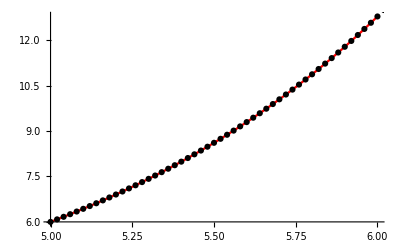

```mathematica
(*Въвеждаме условието на задачата*)
a = 5.; b = 6.;
x = a;
y = 6.;
points = {{x,y}};
f[x_,y_]:=y-Log[x^2+1]+(2x)/(x^2+1)+1

(*Точно решение*)
yt[x_]:=(-ⅇ^5+7 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5

(*Съставяме мрежата*)
h = 0.02; n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1=h*f[x,y];
k2=h*f[x+1/2 h,y+1/2 k1];
k3=h*f[x+1/2 h,y+1/2 k2];
k4=h*f[x+h,y+k3];
Print["i = ", i, ", x_i = ",x, ", y_i = ",y, ", k1 = , ",k1,", k2 = ",k2,", k3 = ",k3,", k4 = ",k4,", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", Истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### в) Каква е теоретичната грешна на полученото приближено решение?

```mathematica
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Теоретичната локална  грешка е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

### г) Каква би била точността при използване на модифицирания метод на Ойлер за поставената задача със същата стъпка? Направете сравнение между двата метода.

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална грешка  е 0.0004

Теоретичната глобална грешка е 0.02

i = 0, x_i = 5., y_i = 6., f_i = 4.12652, x_(i + 1/2) = 5.01, y_(i + 1/2) = 6.04127, f_(i + 1/2) = 4.16323 , y_точно = 6., Истинска грешка = 8.88178×10^-16

i = 1, x_i = 5.02, y_i = 6.08326, f_i = 4.20069, x_(i + 1/2) = 5.03, y_(i + 1/2) = 6.12527, f_(i + 1/2) = 4.23816 , y_точно = 6.08327, Истинска грешка = 4.95163×10^-6

i = 2, x_i = 5.04, y_i = 6.16803, f_i = 4.2764, x_(i + 1/2) = 5.05, y_(i + 1/2) = 6.21079, f_(i + 1/2) = 4.31465 , y_точно = 6.16804, Истинска грешка = 0.000010105

i = 3, x_i = 5.06, y_i = 6.25432, f_i = 4.35367, x_(i + 1/2) = 5.07, y_(i + 1/2) = 6.29786, f_(i + 1/2) = 4.39272 , y_точно = 6.25434, Истинска грешка = 0.0000154662

i = 4, x_i = 5.08, y_i = 6.34218, f_i = 4.43255, x_(i + 1/2) = 5.09, y_(i + 1/2) = 6.3865, f_(i + 1/2) = 4.4724 , y_точно = 6.3422, Истинска грешка = 0.0000210416

i = 5, x_i = 5.1, y_i = 6.43162, f_i = 4.51305, x_(i + 1/2) = 5.11, y_(i + 1/2) = 6.47675, f_(i + 1/2) = 4.55373 , y_точно = 6.43165, Истинска грешка = 0.0000268375

i = 6, x_i = 5.12, y_i = 6.5227, f_i = 4.59522, x_(i + 1/2) = 5.13, y_(i + 1/2) = 6.56865, f_(i + 1/2) = 4.63674 , y_точно = 6.52273, Истинска грешка = 0.0000328606

i = 7, x_i = 5.14, y_i = 6.61543, f_i = 4.67909, x_(i + 1/2) = 5.15, y_(i + 1/2) = 6.66222, f_(i + 1/2) = 4.72146 , y_точно = 6.61547, Истинска грешка = 0.0000391178

i = 8, x_i = 5.16, y_i = 6.70986, f_i = 4.76469, x_(i + 1/2) = 5.17, y_(i + 1/2) = 6.75751, f_(i + 1/2) = 4.80793 , y_точно = 6.70991, Истинска грешка = 0.0000456159

i = 9, x_i = 5.18, y_i = 6.80602, f_i = 4.85205, x_(i + 1/2) = 5.19, y_(i + 1/2) = 6.85454, f_(i + 1/2) = 4.89618 , y_точно = 6.80607, Истинска грешка = 0.0000523622

i = 10, x_i = 5.2, y_i = 6.90394, f_i = 4.94121, x_(i + 1/2) = 5.21, y_(i + 1/2) = 6.95336, f_(i + 1/2) = 4.98626 , y_точно = 6.904, Истинска грешка = 0.0000593641

i = 11, x_i = 5.22, y_i = 7.00367, f_i = 5.03221, x_(i + 1/2) = 5.23, y_(i + 1/2) = 7.05399, f_(i + 1/2) = 5.07818 , y_точно = 7.00374, Истинска грешка = 0.000066629

i = 12, x_i = 5.24, y_i = 7.10523, f_i = 5.12508, x_(i + 1/2) = 5.25, y_(i + 1/2) = 7.15648, f_(i + 1/2) = 5.172 , y_точно = 7.10531, Истинска грешка = 0.0000741648

i = 13, x_i = 5.26, y_i = 7.20867, f_i = 5.21987, x_(i + 1/2) = 5.27, y_(i + 1/2) = 7.26087, f_(i + 1/2) = 5.26775 , y_точно = 7.20875, Истинска грешка = 0.0000819794

i = 14, x_i = 5.28, y_i = 7.31403, f_i = 5.31661, x_(i + 1/2) = 5.29, y_(i + 1/2) = 7.36719, f_(i + 1/2) = 5.36547 , y_точно = 7.31412, Истинска грешка = 0.000090081

i = 15, x_i = 5.3, y_i = 7.42134, f_i = 5.41533, x_(i + 1/2) = 5.31, y_(i + 1/2) = 7.47549, f_(i + 1/2) = 5.4652 , y_точно = 7.42144, Истинска грешка = 0.000098478

i = 16, x_i = 5.32, y_i = 7.53064, f_i = 5.51608, x_(i + 1/2) = 5.33, y_(i + 1/2) = 7.5858, f_(i + 1/2) = 5.56698 , y_точно = 7.53075, Истинска грешка = 0.000107179

i = 17, x_i = 5.34, y_i = 7.64198, f_i = 5.6189, x_(i + 1/2) = 5.35, y_(i + 1/2) = 7.69817, f_(i + 1/2) = 5.67085 , y_точно = 7.6421, Истинска грешка = 0.000116193

i = 18, x_i = 5.36, y_i = 7.7554, f_i = 5.72384, x_(i + 1/2) = 5.37, y_(i + 1/2) = 7.81264, f_(i + 1/2) = 5.77685 , y_точно = 7.75552, Истинска грешка = 0.000125529

i = 19, x_i = 5.38, y_i = 7.87093, f_i = 5.83093, x_(i + 1/2) = 5.39, y_(i + 1/2) = 7.92924, f_(i + 1/2) = 5.88502 , y_точно = 7.87107, Истинска грешка = 0.000135196

i = 20, x_i = 5.4, y_i = 7.98864, f_i = 5.94021, x_(i + 1/2) = 5.41, y_(i + 1/2) = 8.04804, f_(i + 1/2) = 5.99542 , y_точно = 7.98878, Истинска грешка = 0.000145204

i = 21, x_i = 5.42, y_i = 8.10854, f_i = 6.05173, x_(i + 1/2) = 5.43, y_(i + 1/2) = 8.16906, f_(i + 1/2) = 6.10807 , y_точно = 8.1087, Истинска грешка = 0.000155562

i = 22, x_i = 5.44, y_i = 8.23071, f_i = 6.16554, x_(i + 1/2) = 5.45, y_(i + 1/2) = 8.29236, f_(i + 1/2) = 6.22304 , y_точно = 8.23087, Истинска грешка = 0.000166281

i = 23, x_i = 5.46, y_i = 8.35517, f_i = 6.28169, x_(i + 1/2) = 5.47, y_(i + 1/2) = 8.41798, f_(i + 1/2) = 6.34036 , y_точно = 8.35534, Истинска грешка = 0.000177371

i = 24, x_i = 5.48, y_i = 8.48197, f_i = 6.40021, x_(i + 1/2) = 5.49, y_(i + 1/2) = 8.54598, f_(i + 1/2) = 6.46008 , y_точно = 8.48216, Истинска грешка = 0.000188843

i = 25, x_i = 5.5, y_i = 8.61117, f_i = 6.52116, x_(i + 1/2) = 5.51, y_(i + 1/2) = 8.67639, f_(i + 1/2) = 6.58225 , y_точно = 8.61138, Истинска грешка = 0.000200708

i = 26, x_i = 5.52, y_i = 8.74282, f_i = 6.64458, x_(i + 1/2) = 5.53, y_(i + 1/2) = 8.80927, f_(i + 1/2) = 6.70692 , y_точно = 8.74303, Истинска грешка = 0.000212976

i = 27, x_i = 5.54, y_i = 8.87696, f_i = 6.77053, x_(i + 1/2) = 5.55, y_(i + 1/2) = 8.94466, f_(i + 1/2) = 6.83415 , y_точно = 8.87718, Истинска грешка = 0.000225659

i = 28, x_i = 5.56, y_i = 9.01364, f_i = 6.89905, x_(i + 1/2) = 5.57, y_(i + 1/2) = 9.08263, f_(i + 1/2) = 6.96397 , y_точно = 9.01388, Истинска грешка = 0.000238769

i = 29, x_i = 5.58, y_i = 9.15292, f_i = 7.0302, x_(i + 1/2) = 5.59, y_(i + 1/2) = 9.22322, f_(i + 1/2) = 7.09645 , y_точно = 9.15317, Истинска грешка = 0.000252318

i = 30, x_i = 5.6, y_i = 9.29485, f_i = 7.16403, x_(i + 1/2) = 5.61, y_(i + 1/2) = 9.36649, f_(i + 1/2) = 7.23164 , y_точно = 9.29512, Истинска грешка = 0.000266319

i = 31, x_i = 5.62, y_i = 9.43948, f_i = 7.3006, x_(i + 1/2) = 5.63, y_(i + 1/2) = 9.51249, f_(i + 1/2) = 7.36958 , y_точно = 9.43976, Истинска грешка = 0.000280783

i = 32, x_i = 5.64, y_i = 9.58687, f_i = 7.43995, x_(i + 1/2) = 5.65, y_(i + 1/2) = 9.66127, f_(i + 1/2) = 7.51035 , y_точно = 9.58717, Истинска грешка = 0.000295725

i = 33, x_i = 5.66, y_i = 9.73708, f_i = 7.58216, x_(i + 1/2) = 5.67, y_(i + 1/2) = 9.8129, f_(i + 1/2) = 7.65399 , y_точно = 9.73739, Истинска грешка = 0.000311157

i = 34, x_i = 5.68, y_i = 9.89016, f_i = 7.72726, x_(i + 1/2) = 5.69, y_(i + 1/2) = 9.96743, f_(i + 1/2) = 7.80056 , y_точно = 9.89049, Истинска грешка = 0.000327093

i = 35, x_i = 5.7, y_i = 10.0462, f_i = 7.87532, x_(i + 1/2) = 5.71, y_(i + 1/2) = 10.1249, f_(i + 1/2) = 7.95012 , y_точно = 10.0465, Истинска грешка = 0.000343547

i = 36, x_i = 5.72, y_i = 10.2052, f_i = 8.02641, x_(i + 1/2) = 5.73, y_(i + 1/2) = 10.2854, f_(i + 1/2) = 8.10273 , y_точно = 10.2055, Истинска грешка = 0.000360534

i = 37, x_i = 5.74, y_i = 10.3672, f_i = 8.18058, x_(i + 1/2) = 5.75, y_(i + 1/2) = 10.449, f_(i + 1/2) = 8.25845 , y_точно = 10.3676, Истинска грешка = 0.000378068

i = 38, x_i = 5.76, y_i = 10.5324, f_i = 8.33789, x_(i + 1/2) = 5.77, y_(i + 1/2) = 10.6158, f_(i + 1/2) = 8.41735 , y_точно = 10.5328, Истинска грешка = 0.000396165

i = 39, x_i = 5.78, y_i = 10.7007, f_i = 8.49841, x_(i + 1/2) = 5.79, y_(i + 1/2) = 10.7857, f_(i + 1/2) = 8.57949 , y_точно = 10.7012, Истинска грешка = 0.000414841

i = 40, x_i = 5.8, y_i = 10.8723, f_i = 8.6622, x_(i + 1/2) = 5.81, y_(i + 1/2) = 10.959, f_(i + 1/2) = 8.74493 , y_точно = 10.8728, Истинска грешка = 0.00043411

i = 41, x_i = 5.82, y_i = 11.0472, f_i = 8.82933, x_(i + 1/2) = 5.83, y_(i + 1/2) = 11.1355, f_(i + 1/2) = 8.91374 , y_точно = 11.0477, Истинска грешка = 0.00045399

i = 42, x_i = 5.84, y_i = 11.2255, f_i = 8.99986, x_(i + 1/2) = 5.85, y_(i + 1/2) = 11.3155, f_(i + 1/2) = 9.086 , y_точно = 11.226, Истинска грешка = 0.000474497

i = 43, x_i = 5.86, y_i = 11.4072, f_i = 9.17386, x_(i + 1/2) = 5.87, y_(i + 1/2) = 11.499, f_(i + 1/2) = 9.26175 , y_точно = 11.4077, Истинска грешка = 0.000495648

i = 44, x_i = 5.88, y_i = 11.5925, f_i = 9.35141, x_(i + 1/2) = 5.89, y_(i + 1/2) = 11.686, f_(i + 1/2) = 9.44109 , y_точно = 11.593, Истинска грешка = 0.000517462

i = 45, x_i = 5.9, y_i = 11.7813, f_i = 9.53257, x_(i + 1/2) = 5.91, y_(i + 1/2) = 11.8766, f_(i + 1/2) = 9.62408 , y_точно = 11.7818, Истинска грешка = 0.000539956

i = 46, x_i = 5.92, y_i = 11.9738, f_i = 9.71742, x_(i + 1/2) = 5.93, y_(i + 1/2) = 12.0709, f_(i + 1/2) = 9.81079 , y_точно = 11.9743, Истинска грешка = 0.000563149

i = 47, x_i = 5.94, y_i = 12.17, f_i = 9.90604, x_(i + 1/2) = 5.95, y_(i + 1/2) = 12.269, f_(i + 1/2) = 10.0013 , y_точно = 12.1706, Истинска грешка = 0.00058706

i = 48, x_i = 5.96, y_i = 12.37, f_i = 10.0985, x_(i + 1/2) = 5.97, y_(i + 1/2) = 12.471, f_(i + 1/2) = 10.1957 , y_точно = 12.3706, Истинска грешка = 0.000611708

i = 49, x_i = 5.98, y_i = 12.5739, f_i = 10.2949, x_(i + 1/2) = 5.99, y_(i + 1/2) = 12.6769, f_(i + 1/2) = 10.394 , y_точно = 12.5746, Истинска грешка = 0.000637114

i = 50, x_i = 6., y_i = 12.7818, f_i = 10.4952, x_(i + 1/2) = 6.01, y_(i + 1/2) = 12.8868, f_(i + 1/2) = 10.5964 , y_точно = 12.7825, Истинска грешка = 0.000663298

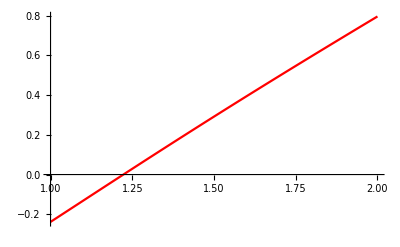

```mathematica
(*Въвеждаме условието на задачата*)
a = 5.;b=6.;
x = a;
y = 6.;
points = {{x,y}};
f[x_,y_] :=y-Log[x^2+1]+(2x)/(x^2+1)+1

(*Точно решение*)
yt[x_] := (-ⅇ^5+7 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5

(*Съставяме мрежата*)
h = 0.02; n = (b-a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, ", x_i = ", x, ", y_i = ", y, ", f_i = ", f[x,y]  , ", x_(i + 1/2) = ", x12, ", y_(i + 1/2) = ", y12, ", f_(i + 1/2) = ", f[x12,y12]  ", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, 1, 2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```